# Report: Project 1

Date: 2022-11-28

# Part 1:

## Summary

### Task

a)  	1. Write received signal r(t) in the form A(d)cos(2πfc + ϕ(d)).
	    And express the power of the received signal as a function of d.
	2.  Plot the power between d = 0, to d = 2 km. One in linear scale, and one in dB.

b)	      Repeat step two, but account for propagation loss in the power function.

### Result

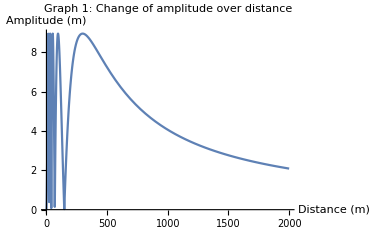

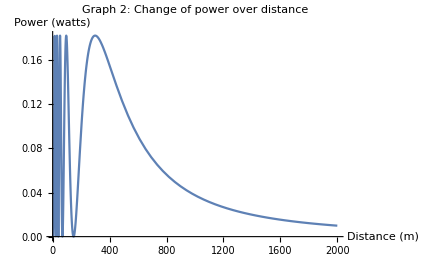
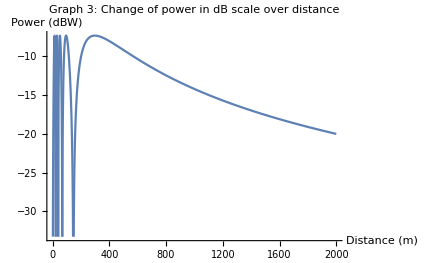

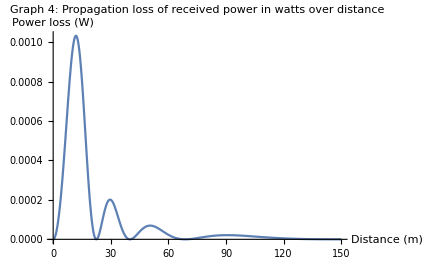
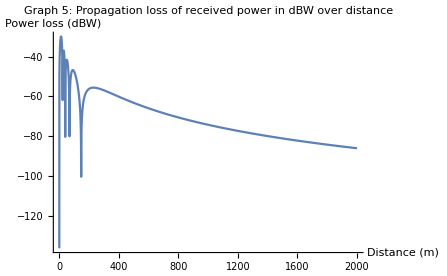

## Explaining the methods

First, the figure in the question was broken down into a simple diagram as shown below. The radio tower is represented by the dot on the top left and the mobile radio unit is shown by the dot in the middle right. The reflected and direct signals are demonstrated by the arrows. The extension of the reflected signal was then used to form a triangle. The hypotenuse of this triangle was used to calculate the direct path of the wave.  
-Graphics-

The frequency of the received signal, r(t)=s(t-τ1)-s(t-τ2), was used alongside equation: s(t)=√Pcos(2fc t)to calculate the real and imaginary parts of the reflected wave. The details of the calculations are shown in the Code section. The amplitude and the phase shift of the wave was calculated using trigonometry and this was then used to plot the graph showing how the amplitude varied over a distance of 0 to 2km. 

Additionally, the wavelength was then figured out by the frequency and the speed of the wave. The equations of power and propagation due to power loss was used to plot graphs.

## Discussing the results

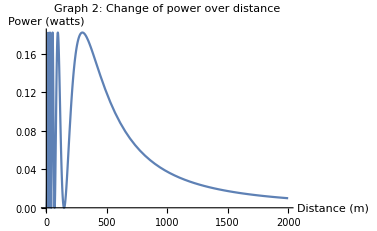
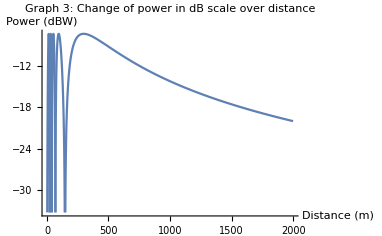
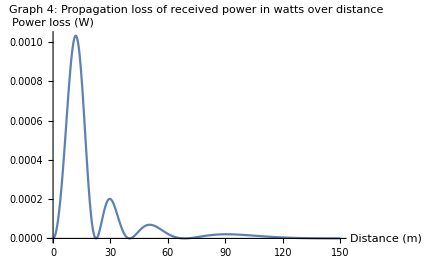
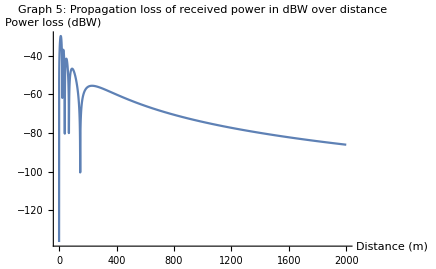
-Graphics-
The first graph shows how the amplitude of the sinus wave varies over a distance of 0 to 2km. From the graph it is noted that around 300m the amplitude of the wave begins to drop and goes towards zero. This is called the turning point of the curve and from the equation used it can be seen that during this point the real and imaginary parts cancel out themselves. 


-Graphics-                                                -Graphics-

Graphs 2 and 3 show how the change of power received over distance. From the two graphs it seems that power reduces when distance is increased. Form graph 2 it is seen that the power oscillates up to a distance of 300 meters and then starts dropping. By looking at the given equation, it is deemed that this is a result of the change of amplitude, power is proportional to the power of the amplitude. So as the amplitude drops the power also drops. The decibel watts demonstration in graph 3 follows a logarithmic scale. This makes it easier to draw comparisons, as the values of power can now be compared to a fixed constant, 1W. 


-Graphics-              -Graphics-

Graphs 4 and 5 demonstrates the decaying of propagation power loss. From graph 4 it seen that the power received decreases exponentially as the distance increases. This is because power loss is inversely proportional to the square of the distance. As a result as the distance is doubled the power is reduced quadratically. This means that as distance increases the signal strength is reduced drastically. The logarithmic scale in graph 5 helps to compare the power loss and this helps to draw suitable conclusions.

## Code section

```mathematica
P=20; (*dBW, 100 watts*)
```

```mathematica
Fc=500 *10^6; (*MHz*)
```

```mathematica
s[t_]:=√P Cos[2 π Fc t ]
```

```mathematica
c=3*10^8; (*speed of light*)
```

```mathematica
(*Figure of radio tower and mobile radio unit.*)
(*Shows direct signal, and reflected signal*)
(*The reflected signal can be extended down into a triangle to obtain the hypotenuse*)
```

```mathematica
-Graphics-
(*Dividing the hypotenuse by c, the time delay is obtained*)
```

```mathematica
τ1=(√(d^2+28.5^2))/c;(*time delay, direct path*)
```

```mathematica
τ2=(√(d^2+31.5^2))/c;(*time delay, reflected path*)
```

```mathematica
r[t_]:=s[(t-τ1)]-s[(t-τ2)] (*recived signal*)
```

```mathematica
r[t]
```

2 √5 Cos[1000000000 π (-(√(812.25+d^2))/300000000+t)]-2 √5 Cos[1000000000 π (-(√(992.25+d^2))/300000000+t)]

```mathematica
(*phasor in polar form*)
```

```mathematica
Polar1=2 √5 (Cos[2π Fc  (-(√(812.25+d^2))/c)]-ⅈ Sin[2π Fc  (-(√(812.25+d^2))/c)]); (*phasor in polar form*)
```

```mathematica
Polar2=2 √5 (Cos[2π Fc  (-(√(992.25+d^2))/c)]-ⅈ Sin[2π Fc  (-(√(992.25+d^2))/c)]);
```

```mathematica
(*real phasor addition*)
```

```mathematica
real=2 √5(Cos[2π Fc (-(√(812.25+d^2))/c)]- Cos[2π Fc  (-(√(992.25+d^2))/c)]);
```

```mathematica
(*imaginary phasor addition*)
```

```mathematica
im=2 √5(-Sin[2π Fc (-(√(812.25+d^2))/c)]+Sin[2π Fc  (-(√(992.25+d^2))/c)]);
```

```mathematica
Amp=√(real^2+im^2); (*amplitude, A(d)*)
Phi=ArcTan[im/real]; (*phase, phi(d)*)
```

```mathematica
Rpow[t_]:=Amp Cos[2π Fc t + Phi]; (*Signal r(d) in A(d)Cos(2π Fc t + Phi(d)) form*)
```

```mathematica
Rpow[t]
```

Cos[1000000000 π t+ArcTan[(Sin[10/3 √(812.25+d^2) π]-Sin[10/3 √(992.25+d^2) π])/(Cos[10/3 √(812.25+d^2) π]-Cos[10/3 √(992.25+d^2) π])]] √(20 (Cos[10/3 √(812.25+d^2) π]-Cos[10/3 √(992.25+d^2) π])^2+20 (Sin[10/3 √(812.25+d^2) π]-Sin[10/3 √(992.25+d^2) π])^2)

```mathematica
(*plot of amplitude*)
```

```mathematica
Plot[Amp,{d,0,2000},AxesLabel->{"Distance (m)","Amplitude (m)"}, PlotLabel->"Graph 1: Change of amplitude over distance"]
```

-Graphics-

```mathematica
λ=c/Fc; (*radio-wavelength*)
```

```mathematica
power=λ^2/(4π)^2 Amp^2; (*power of recived signal*)
```

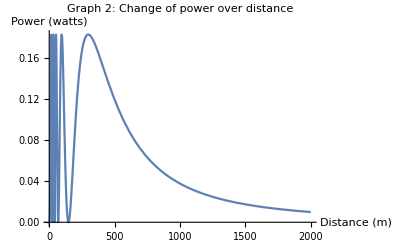

```mathematica
Plot[power,{d,0,2000},AxesLabel->{"Distance (m)","Power (watts)"}, PlotLabel->"Graph 2: Change of power over distance"] (*power, linear*)
```

```mathematica
DB=10Log10[power];
```

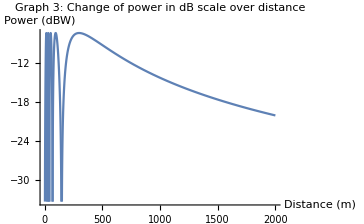

```mathematica
Plot[DB,{d,0,2000},AxesLabel->{"Distance (m)","Power (dBW)"}, PlotLabel->"Graph 3: Change of power in dB scale over distance"] (*power, dB scale*)
```

```mathematica
(*Del b) med decay*)
```

```mathematica
powerdecay=λ^2/((4π)^2*d^2)Amp^2; (*power*)
```

```mathematica
Plot[powerdecay,{d,0,150},PlotRange -> Full, AxesLabel->{"Distance (m)","Power loss (W)"}, PlotLabel->"Graph 4: Propagation loss of received power in watts over distance"] (*power, with decay*)
```

-Graphics-

```mathematica
DBdecay=10Log10[powerdecay];
```

```mathematica
Plot[DBdecay,{d,0,2000}, AxesLabel->{"Distance (m)","Power loss (dBW)"}, PlotLabel->"Graph 5: Propagation loss of received power in dBW over distance"] (*power, dB scale with decay*)
```

-Graphics-